## 1. 数据准备

### 1.1. 数据来源

Terra/Aqua卫星MODIS传感器数据反演所得的净初级生产力(NPP)逐年数据

产品MOD17A3H v006由美国地质调查局(USGS)生产和托管(DOI: 10.5067/MODIS/MOD17A3H.006)

int16类型

NPP结果单位为kg C/m.b2, 并缩小到10^-4倍

部分未计算NPP的像元根据性质被赋值32761~32767

### 1.2. 数据导入与异常值移除

时间范围 : 2004 年~2015 年

更正了异常值移除规则中的错误, 原有的异常值移除规则已被注释, 不再执行. (2024-09-19)

```mathematica
ts=Import[NotebookDirectory[]<>"../Source/MOD17A3H_Lyr_Stk.tif"]//ImageData[#,"Bit16"]&//Part[#,All,All,5;;16]&//Flatten[#,1]&;
ts-=32768;
(*ts=DeleteCases[ts,{_,(_?(#>32760&))..,_}];*)
ts=Select[ts,!MemberQ[#,_?(#>32760&)]&];
```

```mathematica
ts//Length
```

1338967

## 2. 仅考虑时间因素的回归模型

### 2.1. 利用前n年NPP预测下一年NPP: n元线性回归模型

#### 2.1.1. 训练样本选取

不放回随机抽取二十万个样本, 样本的空间分布完全随机, 抽取结果中十六万个样本被用作训练集, 四万个样本被用作测试集, 二者互斥.

```mathematica
(*Use DOI of data to initialize the random seed. *)
SeedRandom["10.5067/MODIS/MOD17A3H.006"]
tssmp=ts//RandomSample[#,200000]&//N;
train=tssmp[[1;;160000]];
test=tssmp[[160001;;-1]];
```

#### 2.1.2. 模型假设

每个像元所在位置, 在t_(n+1)时刻的NPP值, 只和该位置t_1, t_2, …, t_n时刻的NPP值有关, 与其他像元任何时间的NPP值均无关

参与模型训练的数据规模远大于模型的复杂程度, 不需要正则化

#### 2.1.3. 模型建立方法

使用训练集中的最后(n+1)年至最后2年的数据作为自变量, 最后一年的数据作为因变量, 构造n元线性回归模型

```mathematica
linRegSpat//ClearAll;
linRegSpat[year_]:=linRegSpat[year]=Block[{n=year,varReg,mdlReg},
	varReg=Table[Unique["x"],{n}];
	mdlReg=train[[All,-(n+1);;-1]]//LinearModelFit[#,varReg,varReg]&;
	Return[mdlReg];
];
```

计算回归结果R^2, 并绘制R^2与参与回归分析的数据年数n之间的关系图

{0.848504,0.855523,0.889383,0.889478,0.897886,0.900578,0.900581,0.900879,0.903732,0.903894}

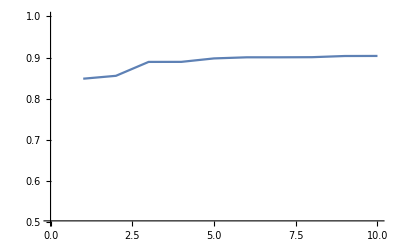

```mathematica
With[{linRegSpatR2=Table[linRegSpat[n]["RSquared"],{n,10}]},
	Print[linRegSpatR2];
	Print[ListPlot[linRegSpatR2,Joined->True,PlotRange->{{0, 10},{0.5,1}}]];
]
```

#### 2.1.4. 模型泛化能力测试

使用测试集中的最后(n+1)年至最后2年的数据作为自变量, 预报最后一年的数据

将预报结果与测试集中实际的数据比较, 计算RMSE

```mathematica
linRegSpatFunc//ClearAll;
linRegSpatFunc[year_]:=linRegSpatFunc[year]=linRegSpat[year]["Function"];
```

```mathematica
linRegSpatRMSE//ClearAll;
linRegSpatRMSE[year_]:=linRegSpatRMSE[year]=Block[{n=year,err,fn},
	fn=linRegSpatFunc[year];
	err=Map[(fn@@Most[#]-Last[#])&,test[[All,-(n+1);;-1]]];
	Return[err^2//Mean//Sqrt];
];
```

计算均方根误差RMSE, 并绘制RMSE与参与回归分析的数据年数n之间的关系图

{438.726,428.16,373.707,373.669,359.395,354.86,354.854,354.373,349.779,349.472}

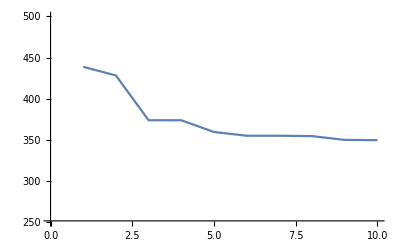

```mathematica
Print[Table[linRegSpatRMSE[n],{n,10}]];
Print[ListPlot[Table[linRegSpatRMSE[n],{n,10}],Joined->True,PlotRange->{{0, 10},{250,500}}]];
```

### 2.2. 分段趋势分析: 分段线性回归模型(拟合结果不用于预测)

```mathematica
(*Use DOI of data to initialize the random seed. *)
SeedRandom["10.5067/MODIS/MOD17A3H.006"]
smpReg=RandomSample[ts,20];
```

#### 2.2.1. 绝对值函数与一次函数的线性组合

考虑分段线性回归模型
y=Piecewise[{{k_0(x-x_1)+y_1, x<x_1}, {k_1(x-x_1)+y_1, x≥x_1}}], (k_0,k_1∈ℝ)
该回归方程可视为y=1, y=x, 以及y=|x-x_1|三者的线性组合.

在给定分段点横坐标x_1的情况下, 可以确定回归模型中的三个参数. 但不同的x_1拟合效果不同.

```mathematica
linpwReg//Clear;
linpwReg[tser_,x1_]:=Block[{x},LinearModelFit[tser,{x,Abs[x-x1]},x]]
```

要寻找最佳的分段点, 需要建立回归方程R^2与x_1的关系, 并通过最优化算法, 求得使R^2取最大时的x_1

```mathematica
linpwRegRsq//Clear;
linpwRegRsq[tser_,x1_]:=Block[{x,fn,residue},
	Return[linpwReg[tser,x1]["RSquared"]];
];
```

最优化算法是基于迭代的, 不能并行化. 当时相数目为12时, 估测每百次优化的平均开销达到了秒级, 对于常用的时序产品, 其像元数目一般在10^5至10^8的数量级, 处理时间预计可达数小时至数日, 效率过低, 因此需要采用其他方法.

```mathematica
perfMax=Table[Table[Flatten[{mthd,FindMaximum[linpwRegRsq[smpReg[[idx]],x1],{x1,6.5},Method->mthd]//AbsoluteTiming},2],{mthd,{Automatic,"ConjugateGradient","PrincipalAxis","LevenbergMarquardt","Newton","QuasiNewton"}}]//TableForm,
{idx,1,smpReg//Length,1}];
Manipulate[perfMax[[idx]],{idx,1,perfMax//Length,1}]
```

#### 2.2.2. 引入虚拟变量^[1], 将分段回归转化为二元回归^[1]

参考文献: 
	[1]孔凡胜. 西藏旅游人口的分段回归分析[J]. 现代商贸工业, 2019, 40(03): 24-25. DOI:10.19311/j.cnki.1672-3198.2019.03.011.
	[2]高璇, 赵东升, 郑度. 1961～2018年中国地表温度变化的区域差异[J]. 大气科学, 2023, 47(04): 995-1006.

分段线性回归的方程可做如下变形^[1-2]: 
y=Piecewise[{{β_0+β_1 x, x<x_1}, {β_0+β_1 x+β_2(x-x_1), x≥x_1}}],

令{ξ_1=x
ξ_2=max(x-x_1,0), 则上式变形为关于ξ_1, ξ_2的二元回归方程y=β_0+β_1 ξ_1+β_2 ξ_2

但是, 上述方法需要手动指定分段点的横坐标, 于是上述问题转化为2.2.1中的问题. 需要寻找一种高效的自适应搜索分段点横坐标的方法.

#### 2.2.3. 分段点搜索算法

在GIthub可检索到一系列具有分段回归功能的程序包. 其中, 由Google维护的pwlfit项目中, 提供了分段回归的分段点自适应搜索功能.

上述项目由Python编写. 由于本课程的项目将在IDL上实现, 需要将项目的主要代码全部转化为IDL代码.

本课程项目将以2021年7月21日的提交版本为准. 主要原因是:

该版本是最后一版在注释中详细提供了与Py 2.x兼容性有关内容的版本.

考虑到项目所依托的ENVI 5.3/IDL 8.5 以及对应的IDL Python Bridge, 可能与ArcGIS Desktop 10.5 的arcpy一同被集成至独立的python 2. x环境下使用,

代码中需要注明源代码的来源.

## 3. 时间序列特征提取

当时间序列包含的时相数量在10~100的数量级时, 时间序列的周期性变化特征一般不能使用FFT方法提取, 主要原因:

在边缘附近容易出现Gibbs效应

如作加窗处理, 易导致失真.

采用各阶自相关函数分析时间序列的波动特征, 并识别出各像元时间序列中, 自相关函数最大的阶.

```mathematica
tsAutoCorr=ParallelTable[CorrelationFunction[smp,{1,10}],{smp,tssmp}];
```

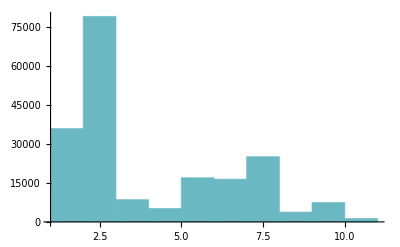

```mathematica
Position[#,Max[#]][[1,1]]&/@Select[tsAutoCorr,AnyTrue[#,Positive]&]//Histogram
```